```mathematica
traj1R=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение близкое к точному\\traj1.txt", "Table"];
traj2R=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение близкое к точному\\traj2.txt", "Table"];
traj3R=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение близкое к точному\\traj3.txt", "Table"];
traj4R=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение близкое к точному\\traj4.txt", "Table"];
```

```mathematica
Rtraj1={}; Rtraj2={}; Rtraj3={}; Rtraj4={};
For[i=1,i<=Length[traj1R],i++,
AppendTo[Rtraj1,{traj1R⟦i,2⟧,traj1R⟦i,3⟧}];
AppendTo[Rtraj2,{traj2R⟦i,2⟧,traj2R⟦i,3⟧}];
 AppendTo[Rtraj3,{traj3R⟦i,2⟧,traj3R⟦i,3⟧}];
AppendTo[Rtraj4,{traj4R⟦i,2⟧,traj4R⟦i,3⟧}]]
```

```mathematica
traj1=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.1\\traj1.txt", "Table"];
traj2=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.1\\traj2.txt", "Table"];
traj3=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.1\\traj3.txt", "Table"];
traj4=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.1\\traj4.txt", "Table"];
```

```mathematica
traj1[[1,1]]
```

0

```mathematica
Length[traj1R]
```

201

```mathematica
traj11={}; traj22={}; traj33={}; traj44={};
For[i=1,i<=Length[traj1],i++,
AppendTo[traj11,{traj1⟦i,2⟧,traj1⟦i,3⟧}];
AppendTo[traj22,{traj2⟦i,2⟧,traj2⟦i,3⟧}];
 AppendTo[traj33,{traj3⟦i,2⟧,traj3⟦i,3⟧}];
AppendTo[traj44,{traj4⟦i,2⟧,traj4⟦i,3⟧}]]
```

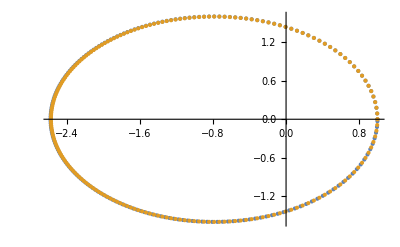
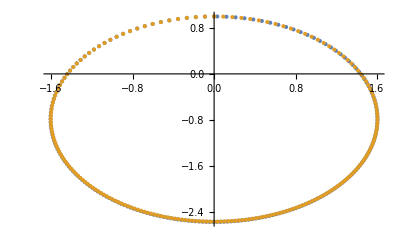
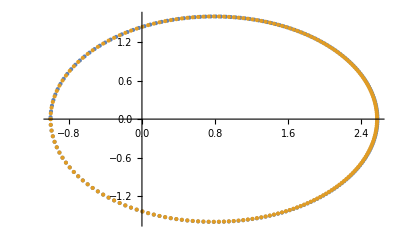
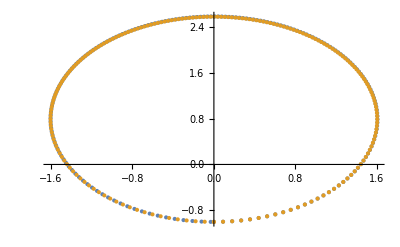

```mathematica
{ListPlot[{traj11,Rtraj1}, ImageSize->400],ListPlot[{traj22,Rtraj2}, ImageSize->400],
ListPlot[{traj33,Rtraj3}, ImageSize->400],ListPlot[{traj44,Rtraj4}, ImageSize->400]}
```

```mathematica
length = Length[Rtraj1];
err1 = Sqrt[{
(Rtraj1⟦length,1⟧ -  traj11⟦length,1⟧ )^2 + (Rtraj1⟦length,2⟧ -  traj11⟦length,2⟧ )^2,
(Rtraj2⟦length,1⟧ -  traj22⟦length,1⟧ )^2 + (Rtraj2⟦length,2⟧ -  traj22⟦length,2⟧ )^2,
(Rtraj3⟦length,1⟧ -  traj33⟦length,1⟧ )^2 + (Rtraj3⟦length,2⟧ -  traj33⟦length,2⟧ )^2,
(Rtraj4⟦length,1⟧ -  traj44⟦length,1⟧ )^2 + (Rtraj4⟦length,2⟧ -  traj44⟦length,2⟧ )^2
}]
```

{0.0313746,0.0313746,0.0313746,0.0313746}

```mathematica
traj1=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.05\\traj1.txt", "Table"];
traj2=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.05\\traj2.txt", "Table"];
traj3=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.05\\traj3.txt", "Table"];
traj4=Import["C:\\Users\\Вячеслав\\Desktop\\параллельные вычисления\\lab4\\Решение с шагом 0.05\\traj4.txt", "Table"];
```

```mathematica
traj11={}; traj22={}; traj33={}; traj44={};
For[i=1,i<=Length[traj1],i++,
AppendTo[traj11,{traj1⟦i,2⟧,traj1⟦i,3⟧}];
AppendTo[traj22,{traj2⟦i,2⟧,traj2⟦i,3⟧}];
 AppendTo[traj33,{traj3⟦i,2⟧,traj3⟦i,3⟧}];
AppendTo[traj44,{traj4⟦i,2⟧,traj4⟦i,3⟧}]]
```

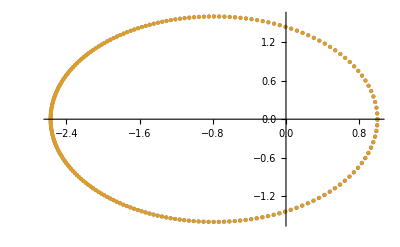
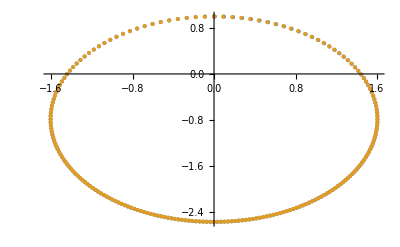
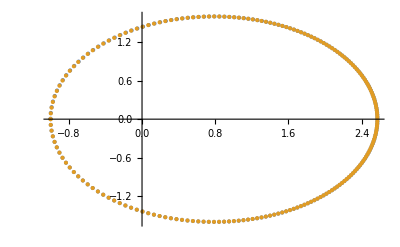
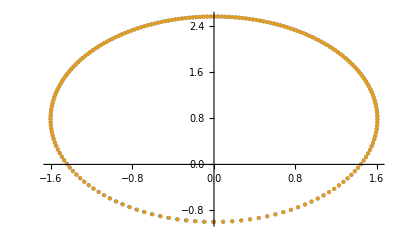

```mathematica
{ListPlot[{traj11,Rtraj1}, ImageSize->400],ListPlot[{traj22,Rtraj2}, ImageSize->400],
ListPlot[{traj33,Rtraj3}, ImageSize->400],ListPlot[{traj44,Rtraj4}, ImageSize->400]}
```

```mathematica
err2= Sqrt[{
(Rtraj1⟦length,1⟧ -  traj11⟦length,1⟧ )^2 + (Rtraj1⟦length,2⟧ -  traj11⟦length,2⟧ )^2,
(Rtraj2⟦length,1⟧ -  traj22⟦length,1⟧ )^2 + (Rtraj2⟦length,2⟧ -  traj22⟦length,2⟧ )^2,
(Rtraj3⟦length,1⟧ -  traj33⟦length,1⟧ )^2 + (Rtraj3⟦length,2⟧ -  traj33⟦length,2⟧ )^2,
(Rtraj4⟦length,1⟧ -  traj44⟦length,1⟧ )^2 + (Rtraj4⟦length,2⟧ -  traj44⟦length,2⟧ )^2
}]
```

{0.00763269,0.00763269,0.00763269,0.00763269}

```mathematica
Log[2,err1/err2]
```

{2.03934,2.03934,2.03934,2.03934}

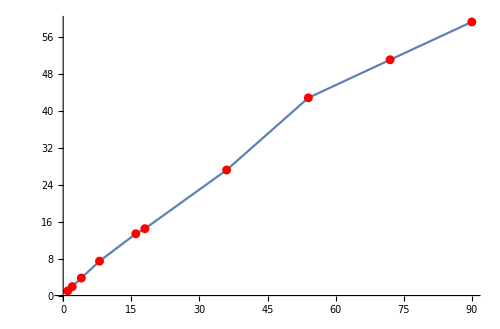

```mathematica
t1 = 3.14984; t2 = 1.63275; t4  = 0.828689; t8 = 0.422312; t16 = 0.234853; t18 = 0.217125;
t36 = 0.115634;  t54 = 0.0734343; t72 = 0.0615789; t90 = 0.0530609; t108 = 0.0444378;
t = {t1,t2,t4,t8,t16,t18,t36,t54,t72,t90,t108};
p ={1,2,4,8,16,18,36,54,72,90,108};
ListS ={};
For[i=0,i<Length[t],i++,AppendTo[ListS,{p⟦i⟧,t1/t⟦i⟧}]]

Show[ListLinePlot[ListS, ImageSize->500,AspectRatio->Automatic],ListPlot[ListS, PlotStyle->Red]]
```